# Ecuaciones de estado

```mathematica
(*Importamos archivos de EoS*)
ClearAll["Global`*"];
SoftRho = Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/Soft.txt", "Table"][[All,1]]; SoftP = Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/Soft.txt", "Table"][[All,2]];
Soft = Transpose[{Flatten[SoftP], Flatten[SoftRho]}];
MidRho = Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/Mid.txt", "Table"][[All,1]]; MidP = Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/Mid.txt", "Table"][[All,2]];
Mid = Transpose[{Flatten[MidP], Flatten[MidRho]}];
StiffRho = Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/Stiff.txt", "Table"][[All,1]]; StiffP = Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/Stiff.txt", "Table"][[All,2]];
Stiff = Transpose[{Flatten[StiffP], Flatten[StiffRho]}];

SLyRho=Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/SLy/rhoSLy.txt","Table"];SLyP=Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/SLy/PSLy.txt","Table"];
SLy=Transpose[{Flatten[SLyP],Flatten[SLyRho]}];
```

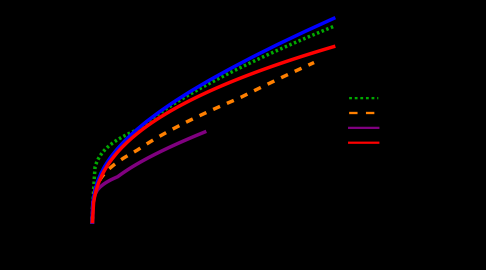

```mathematica
(*Definimos las ecuaciones de estado*)
ρSoft=Quiet[Interpolation[Soft,InterpolationOrder->1]];
ρMid=Quiet[Interpolation[Mid,InterpolationOrder->1]];
ρStiff=Quiet[Interpolation[Stiff,InterpolationOrder->1]];
ρSLy=Quiet[Interpolation[SLy,InterpolationOrder->1]];

f[x_]:=0.035*(0.5x)^(1/2.5)
Toy=Table[{x,f[x]},{x,Min[SoftP],Max[SoftP],(Max[SoftP]-Min[SoftP])/200}];
ρToy=Quiet[Interpolation[Toy,InterpolationOrder->1]];


(* Creamos los plots de cada una *)
SoftPlot=Plot[ρSoft[P],{P,Min[SoftP],Max[SoftP]},PlotStyle->{Darker[Green],Thickness[0.007],Dashing[0.005]}];

MidPlot=Plot[ρMid[P],{P,Min[MidP],Max[MidP]},PlotStyle->{Orange,Thickness[0.007],Dashing[0.015]}];

StiffPlot=Plot[ρStiff[P],{P,Min[StiffP],Max[StiffP]},PlotStyle->{Purple,Thickness[0.007]}];

ToyPlot=Plot[ρToy[P],{P,Min[SoftP],Max[SoftP]},PlotStyle->{Red,Thickness[0.007]}];

SLyPlot=Plot[ρSLy[P],{P,Min[SLyP],Max[SoftP]},PlotStyle->{Blue,Thickness[0.007]}];

(* Mostramos los plots con su leyenda *)
Legended[Show[SoftPlot,MidPlot,StiffPlot,SLyPlot,ToyPlot,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[FontSize->10,Black],FrameLabel->{"P / km^-2","ρ / km^-2"},AspectRatio->3/4,ImageSize->Medium,Background->Transparent,BaseStyle->{FontFamily->"Helvetica",FontSize->12},PlotRange->All],Placed[LineLegend[{{Darker[Green],Thickness[0.007],Dashing[0.005]},{Orange,Thickness[0.007],Dashing[0.015]},Purple, Red},{Style["Soft",10],Style["Middle",10],Style["Stiff",10],Style["Toy",10]},LegendFunction->(Framed[#,FrameStyle->Black,Background->White,FrameMargins->0]&),LegendMarkerSize->{30,2},LabelStyle->(FontFamily->"Helvetica"),Spacings->0.1],{0.17,0.78}]]
```

# Cálculo de Ainit

```mathematica
(*Constantes y valores iniciales*)
Msol=1.4763 (*Factor en unidades naturales*);
rinit=1.0*10^(-15) (*km, todo lo he hecho con 1e-15*);
G=1;
c=1;
κ=8*Pi;

(*Modelo f a utilizar*)
a=-0.05;
fR=a*R[r]^2;
f1R=D[fR,R[r]];
f2R=D[f1R,R[r]];
f3R=D[f2R,R[r]];
fRext=a*Rext[r]^2;
f1Rext=D[fRext,Rext[r]];
f2Rext=D[f1Rext,Rext[r]];
f3Rext=D[f2Rext,Rext[r]];

(*Aquí decidimos qué EoS usar*)
ρ=ρMid;


(*Fijamos la presión central*)
Pinit=7.*10^-4;
Rinit=κ*(ρMid[Pinit]-3*Pinit);

(*Módulo que calcula el valor de A lejos de la estrella dado Ainit*)
Modulo[Ainit_,α_]:=Module[{de1,de2,de3,de4,de5,de6,de7,de,deExt,init,initExt,sol,solExt,rtot,Atot,Btot,Rtot,Atotprime,Btotprime},(*Distancia en radios estelares a la que calculamos A*)(*Ecuaciones diferenciales en el interior de la estrella*)de1=B'[r]==(2 r*B[r])/(3 (1+f1R))*(κ*B[r]*(ρ[P[r]]+3 P[r])+(B[r]/2)*R[r]-(3 A'[r])/(2*r*A[r])+B[r]*fR-f1R*((B[r]/2)*R[r]+(3 A'[r])/(2*r*A[r]))-((3/r)+(3 A'[r])/(2*A[r]))*f2R*R'[r]);
de2=A''[r]==(A'[r]/2)*(B'[r]/B[r]+A'[r]/A[r])+(2 B'[r]*A[r])/(r*B[r])+((2 A[r])/(1+f1R))*(-κ*B[r]*P[r]-B[r]*R[r]/2+((A'[r])/(2 A[r])+2/r)*f2R*R'[r]-(B[r]*fR)/2);
de3=R''[r]==R'[r]*((B'[r])/(2 B[r])-(A'[r])/(2 A[r])-2/r)-((B[r])/(3*f2R))*(κ*(ρ[P[r]]-3 P[r])-(1-f1R)*R[r]-2*fR)-(f3R*R'[r]^2)/f2R;
de4=P'[r]==-((ρ[P[r]]+P[r])/2)*A'[r]/A[r];
de={de1,de2,de3,de4};
init={B[rinit]==1,A'[rinit]==0,P[rinit]==Pinit,R'[rinit]==0,A[rinit]==Ainit,R[rinit]==Rinit,WhenEvent[P[r]<=7*10^(-10),{rtot=r,Atot=A[r],Btot=B[r],Rtot=R[r],Atotprime=A'[r],"StopIntegration"}]};
(*NDSOLVE INTERIOR*)sol=Quiet[NDSolve[{de,init},{P[r],A[r],B[r],R[r]},{r,rinit,500},WorkingPrecision->25,MaxSteps->1000000],{NDSolve::precw,InterpolatingFunction::dmval}];
(*Extraemos las soluciones interiores*)Bder=sol[[1]][[3]]/. Rule->(#2&);
Bprimeder=D[Bder,r];
(*Por algún momento el valor de B en el borde hay que sacarlo así*)Btotprime=Bprimeder/. r->rtot;
(*Ecuaciones diferenciales en el exterior de la estrella*)de5=Bext'[r]==(2 r*Bext[r])/(3 (1+f1Rext))*((Bext[r]/2)*Rext[r]-(3 Aext'[r])/(2*r*Aext[r])+Bext[r]*fRext-f1Rext*((Bext[r]/2)*Rext[r]+(3 Aext'[r])/(2*r*Aext[r]))-((3/r)+(3 Aext'[r])/(2*Aext[r]))*f2Rext*Rext'[r]);
de6=Aext''[r]==(Aext'[r]/2)*(Bext'[r]/Bext[r]+Aext'[r]/Aext[r])+(2 Bext'[r]*Aext[r])/(r*Bext[r])+((2 Aext[r])/(1+f1Rext))*(-Bext[r]*Rext[r]/2+((Aext'[r])/(2 Aext[r])+2/r)*f2Rext*Rext'[r]-(Bext[r]*fRext)/2);
de7=Rext''[r]==Rext'[r]*((Bext'[r])/(2 Bext[r])-(Aext'[r])/(2 Aext[r])-2/r)-((Bext[r])/(3*f2Rext))*(-(1-f1Rext)*Rext[r]-2*fRext)-(f3Rext*Rext'[r]^2)/f2Rext;
deExt={de5,de6,de7};
initExt={Bext[rtot]==Btot,Aext[rtot]==Atot,Rext[rtot]==Rtot,Bext'[rtot]==Btotprime,Aext'[rtot]==Atotprime};
(*NDSOLVE EXTERIOR*)solExt=Quiet[NDSolve[{deExt,initExt},{Aext[r],Bext[r],Rext[r]},{r,rtot,α*rtot},WorkingPrecision->25,MaxSteps->5000000],{NDSolve::precw,InterpolatingFunction::dmval}];
(*Extraemos soluciones exteriores*)AderExt=solExt[[1]][[1]]/. Rule->(#2&);
Arα=AderExt/. r->(α*rtot);
Arα]



(*Lista de radios*)
listaRadios={10,1000,2000,3000,4000};

(*Inicializamos la lista para almacenar los valores buenos*)
listaValoresBuenos={};

(*Inicializamos el valor inicial*)
inicial=0.5;

(*Bucle For para iterar sobre cada elemento de la lista*)
For[i=1,i<=Length[listaRadios],i++,calculo=Modulo[inicial,listaRadios[[i]]];
valorbueno=inicial/calculo;
AppendTo[listaValoresBuenos,valorbueno];
Print["Terminada la integración hasta ",listaRadios[[i]]]
]

(*Juntar las listas en parejas*)
A0=Transpose[{listaRadios,listaValoresBuenos}];
fit=NonlinearModelFit[A0,a1+a2/α^a3,{a1,a2,a3},α]
params={a1,a2,a3}/. fit["BestFitParameters"];
A0infty=params[[1]];
Show[ListPlot[A0,PlotStyle->Red,PlotRange->All],Plot[fit[α],{α,Min[A0[[All,1]]],Max[A0[[All,1]]]},PlotStyle->Blue,PlotRange->All],ImageSize->Large]
Print["El valor extrapolado de Ainit es ",A0infty];

Beep[]
```

Terminada la integración hasta 10

$Aborted

Transpose::nmtx: The first two levels of {{10,1000,2000,3000,4000},{0.0933164}} cannot be transposed.

NonlinearModelFit[Transpose[{{10,1000,2000,3000,4000},{0.0933164}}],a1+a2 α^-a3,{a1,a2,a3},α]

ReplaceAll::reps: {NonlinearModelFit[Transpose[{{10,1000,2000,3000,4000},{0.0933164}}],a1+a2 α^-a3,{a1,a2,a3},α][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Transpose::nmtx: The first two levels of {{10.,1000.,2000.,3000.,4000.},{0.0933164}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{10.,1000.,2000.,3000.,4000.},{0.0933164}}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Transpose[{{10,1000,2000,3000,4000},{0.0933164}}],PlotStyle→color,PlotRange→All],,ImageSize→Large].

Show[ListPlot[Transpose[{{10,1000,2000,3000,4000},{0.0933164}}],PlotStyle→RGBColor[1, 0, 0],PlotRange→All],-Graphics-,ImageSize→Large]

El valor extrapolado de Ainit es {a1,a2,a3}

# Perfiles, coeficientes métricos y escalar de curvatura

Pinit = 7.×10^-4

Radio de la estrella: 11.592389 km

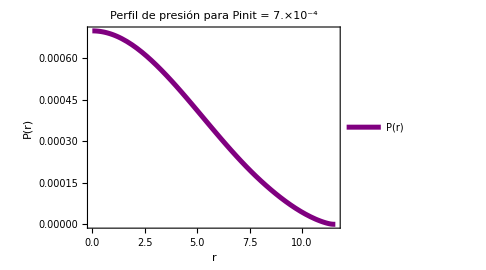
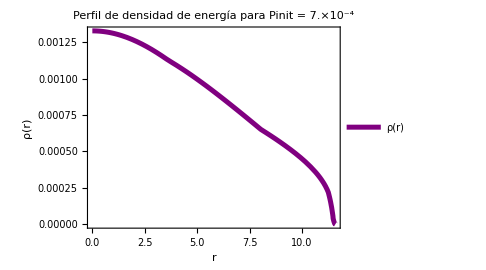

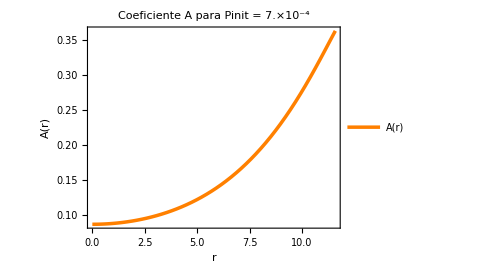
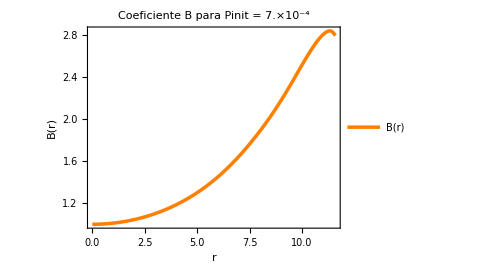

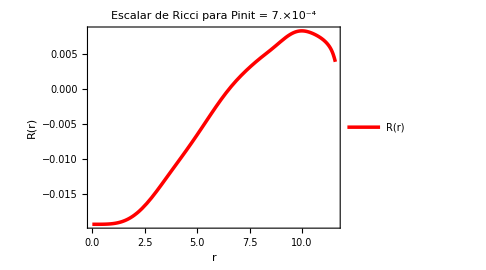

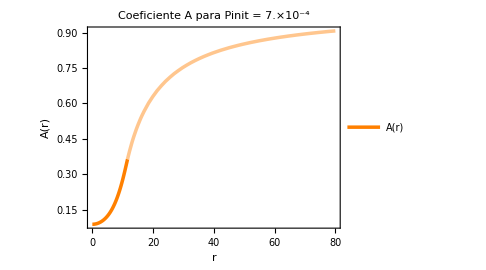
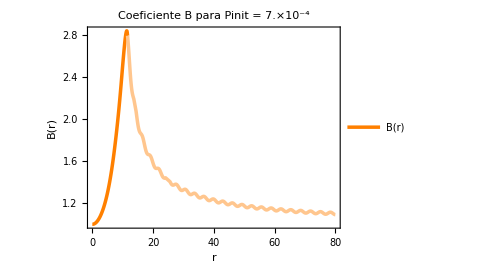

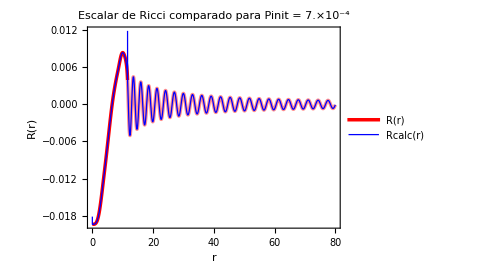

```mathematica
Ainit=0.0873401; (* Sacado del ajuste *)

(* Ecuaciones diferenciales en el interior de la estrella *)
de1=B'[r]==(2r*B[r])/(3 (1+f1R))*(κ*B[r]*(ρ[P[r]]+3 P[r])+(B[r]/2)*R[r]-(3 A'[r])/(2*r*A[r])+B[r]*fR-f1R*((B[r]/2)*R[r]+(3 A'[r])/(2*r*A[r]))-((3/r)+(3 A'[r])/(2*A[r]))*f2R*R'[r]);

de2=A''[r]==(A'[r]/2)*(B'[r]/B[r]+A'[r]/A[r])+(2 B'[r]*A[r])/(r*B[r])+((2 A[r])/(1+f1R))*(-κ*B[r]*P[r]-B[r]*R[r]/2+((A'[r])/(2 A[r])+2/r)*f2R*R'[r]-(B[r]*fR)/2);

de3=R''[r]==R'[r]*((B'[r])/(2 B[r])-(A'[r])/(2 A[r])-2/r)-((B[r])/(3* f2R))*(κ*(ρ[P[r]]-3 P[r])-(1-f1R)*R[r]-2* fR)-(f3R*R'[r]^2)/f2R;

de4=P'[r]==-((ρ[P[r]]+P[r])/2)*A'[r]/A[r];

de={de1,de2,de3,de4};
init={B[rinit]==1,A'[rinit]==0,P[rinit]==Pinit,R'[rinit]==0,A[rinit]==Ainit,R[rinit]==Rinit,WhenEvent[P[r]<=7*10^(-10),{rtot=r,Atot=A[r],Btot=B[r],Rtot=R[r],Atotprime=A'[r],Rtotprime=R'[r],"StopIntegration"}]};

(* NDSOLVE INTERIOR *)
sol=Quiet[NDSolve[{de,init},{P[r],A[r],B[r],R[r]},{r,rinit,50},WorkingPrecision->35,MaxSteps->1000000],{NDSolve::precw,InterpolatingFunction::dmval}];

(* Extraemos las soluciones interiores *)
pder=sol[[1]][[1]]/. Rule->(#2&);
Ader=sol[[1]][[2]]/. Rule->(#2&);
Bder=sol[[1]][[3]]/. Rule->(#2&);
Rder=sol[[1]][[4]]/. Rule->(#2&);
Bprimeder=D[Bder,r];
Bpprimeder=D[Bprimeder,r];
Aprimeder=D[Ader,r];
Apprimeder=D[Aprimeder,r];

(* Valor del radio total de la estrella *)
Print[StringForm["Pinit = ``",DecimalForm[Pinit,ScientificNotationThreshold->{1,1}]]];
Print[StringForm["Radio de la estrella: `` km",NumberForm[rtot,{Infinity,6}]]];


(* Ecuaciones diferenciales en el exterior de la estrella *)
de5=Bext'[r]==(2r*Bext[r])/(3 (1+f1Rext))*((Bext[r]/2)*Rext[r]-(3 Aext'[r])/(2*r*Aext[r])+Bext[r]*fRext-f1Rext*((Bext[r]/2)*Rext[r]+(3 Aext'[r])/(2*r*Aext[r]))-((3/r)+(3 Aext'[r])/(2*Aext[r]))*f2Rext*Rext'[r]);

de6=Aext''[r]==(Aext'[r]/2)*(Bext'[r]/Bext[r]+Aext'[r]/Aext[r])+(2 Bext'[r]*Aext[r])/(r*Bext[r])+((2 Aext[r])/(1+f1Rext))*(-Bext[r]*Rext[r]/2+((Aext'[r])/(2 Aext[r])+2/r)*f2Rext*Rext'[r]-(Bext[r]*fRext)/2);

de7=Rext''[r]==Rext'[r]*((Bext'[r])/(2 Bext[r])-(Aext'[r])/(2 Aext[r])-2/r)-((Bext[r])/(3* f2Rext))*(-(1-f1Rext)*Rext[r]-2* fRext)-(f3Rext*Rext'[r]^2)/f2Rext;

deExt={de5,de6,de7};
initExt={Bext[rtot]==Btot,Aext[rtot]==Atot,Rext[rtot]==Rtot,Rext'[rtot]==Rtotprime,Aext'[rtot]==Atotprime};

(* NDSOLVE EXTERIOR *)
solExt=Quiet[NDSolve[{deExt,initExt},{Aext[r],Bext[r],Rext[r]},{r,rtot,20000},WorkingPrecision->20,MaxSteps->4000000],{NDSolve::precw,InterpolatingFunction::dmval}];

(* Extraemos soluciones exteriores *)
AderExt=solExt[[1]][[1]]/. Rule->(#2&);
BderExt=solExt[[1]][[2]]/. Rule->(#2&);
RderExt=solExt[[1]][[3]]/. Rule->(#2&);
BprimederExt=D[BderExt,r];
BpprimederExt=D[BprimederExt,r];
AprimederExt=D[AderExt,r];
ApprimederExt=D[AprimederExt,r];
RprimederExt=D[AderExt,r];
RpprimederExt=D[RprimederExt,r];

(* Representamos P *)
plotP=Plot[pder,{r,rinit,rtot},PlotStyle->{Purple,Thickness[0.01]},Ticks->{ScientificForm},Frame->True,FrameLabel->{"r","P(r)"},PlotLabel->StringForm["Perfil de presión para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]],AspectRatio->3/4,PlotLegends -> {"P(r)"},ImageSize->Medium,PlotRange->{{0,All},All}];

(* Representamos ρ *)
ρder=ρ[pder];
plotρ=Plot[ρder,{r,rinit,rtot},PlotStyle->{Purple,Thickness[0.01]},Ticks->{ScientificForm},Frame->True,FrameLabel->{"r","ρ(r)"},PlotLabel->StringForm["Perfil de densidad de energía para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]],AspectRatio->3/4,PlotLegends -> {"ρ(r)"},ImageSize->Medium,PlotRange->{{0,All},All}];

(* Hacemos display de estos tres plots *)
Print[plotP, plotρ];

(* Representamos A *)
plotA= Plot[Ader,{r,rinit,rtot},PlotStyle->{Orange,Thickness[0.007]},Ticks->{ScientificForm},Frame->True,FrameLabel->{"r","A(r)"},PlotLabel->StringForm["Coeficiente A para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]],AspectRatio->3/4,PlotLegends -> {"A(r)"},ImageSize->Medium,PlotRange->{{0,All},All}];

(* Representamos B *)
plotB=Plot[Bder,{r,rinit,rtot},PlotStyle->{Orange,Thickness[0.007]},Ticks->{ScientificForm},Frame->True,FrameLabel->{"r","B(r)"},PlotLabel->StringForm["Coeficiente B para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]],AspectRatio->3/4,PlotLegends -> {"B(r)"},ImageSize->Medium,PlotRange->{{0,All},All}];

(* Representamos R *)
plotR=Plot[Rder,{r,rinit,rtot},PlotStyle->{Red,Thickness[0.007]},Ticks->{ScientificForm},Frame->True,FrameLabel->{"r","R(r)"},PlotLabel->StringForm["Escalar de Ricci para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]],AspectRatio->3/4,PlotLegends -> {"R(r)"},ImageSize->Medium,PlotRange->{{0,All},All}];

Print[plotA, plotB];
Print[plotR];

(* Hacemos los plots exteriores y totales *)
plotAext=Plot[AderExt,{r,rtot,80},PlotStyle->{Lighter[Lighter[Orange]],Thickness[0.007]},PlotRange->{{0,All},All}];
plotAtot=Show[plotA,plotAext,PlotRange->All];

plotBext=Plot[BderExt,{r,rtot,80},PlotStyle->{Lighter[Lighter[Orange]],Thickness[0.007]},PlotRange->{{0,All},All}];
plotBtot=Show[plotB,plotBext,PlotRange->All];

plotRext=Plot[RderExt,{r,rtot,80},PlotStyle->{Lighter[Lighter[Red]],Thickness[0.007]},PlotRange->{{0,All},All}];
plotRtot=Show[plotR,plotRext,PlotRange->All];

Print[plotAtot, plotBtot];


(* Comprobamos que el escalar de Ricci está bien calculado comparándolo con el de la ec A5 de Aparicio *)
Rcalc=(Aprimeder/(2*Bder*Ader))*(Bprimeder/Bder+Aprimeder/Ader)-(Apprimeder/(Bder*Ader))-(2*Aprimeder/(r*Bder*Ader))+(2*Bprimeder/(r*Bder^2))-(2/(Bder*r^2))+(2/r^2);
RcalcExt=(AprimederExt/(2*BderExt*AderExt))*(BprimederExt/BderExt+AprimederExt/AderExt)-(ApprimederExt/(BderExt*AderExt))-(2*AprimederExt/(r*BderExt*AderExt))+(2*BprimederExt/(r*BderExt^2))-(2/(BderExt*r^2))+(2/r^2);

plotRcalc=Plot[Rcalc,{r,rinit,rtot},PlotStyle->{Blue,Thickness[0.0025]},PlotLegends -> {"Rcalc(r)"},PlotRange->{{0,All},All}];
plotRcalcExt=Plot[RcalcExt,{r,rtot,80},PlotStyle->{Blue,Thickness[0.0025]},PlotRange->{{0,All},All}];
plotRcalctot=Show[plotRcalc,plotRcalcExt,PlotRange->All];

Show[plotRtot,plotRcalctot,PlotLabel->StringForm["Escalar de Ricci comparado para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]]]

Beep[]
```

```mathematica
npoints=1000;
Int=Table[{rtotX,rtotY},{η,0,2Pi,(ϕmax-0)/(npoints-1)}];
Ext=Table[{r,((0.5 (1-AderExt)-β) r)/(Msol*AderExt*BderExt)},{r,rtot,20000,(20000-rtot)/(npoints-1)}];
Export["/Users/neturo/Desktop/borde_7e-4_0.05.txt",Int,"Table"];
(*Export["/Users/neturo/Desktop/bandamasa_7e-4_0.05.txt",Ext,"Table"];*)
```

# Función de masa

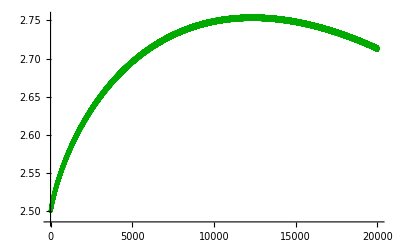

```mathematica
(* Exportamos las funciones obtenidas como tablas de puntos *)
npoints=100000; (* 100000 es un buen número para poder hacer el ajuste luego *)
tabla=Table[{r,0.5*r*(1-Ader)/Msol},{r,rinit,rtot,(rtot-rinit)/(npoints-1)}];
tablaExt=Table[{r,0.5*r*(1-AderExt)/Msol},{r,rtot,20000,(20000-rtot)/(npoints-1)}];
Export["/Users/neturo/Desktop/masa.txt",tablaExt,"Table"];

plotMasaExt=ListLinePlot[tablaExt,PlotStyle->{Darker[Green],Thickness[0.007]},PlotRange->All]

Beep[]

(* (r*(1-Ader))/(Ader*Bder) *)
```

## Masa corregida, masa f(R) y masa asintótica

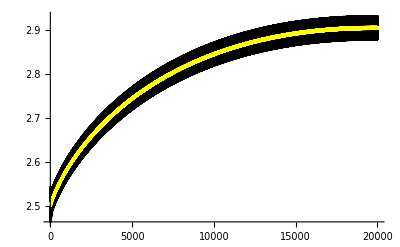

La masa desnuda f(R) para estas condiciones es de 2.49975 masas solares

La masa asintótica f(R) para estas condiciones es de 2.90206 masas solares

```mathematica
masa=Import["/Users/neturo/Desktop/masa.txt","Table"];
(*Realizar el ajuste lineal con ordenada en el origen*)
ajuste=LinearModelFit[masa[[Length[masa]-1000;;Length[masa]]],x,x]; (*Parece que con 1000 puntos está bien para el ajuste*)
β=ajuste["BestFitParameters"][[2]]*Msol ; (* Importante multiplicar β por Msol para devolverlo a km y luego dividirlo todo en los plots *)
lineamasa=Plot[((0.5(1-AderExt)-β)r)/Msol,{r,rtot,20000},PlotPoints->500,PlotStyle->Yellow];
bandamasa=Plot[((0.5 (1-AderExt)-β) r)/(Msol*AderExt*BderExt),{r,rtot,20000},PlotPoints->500,PlotStyle->Black];
plotrecta=Plot[ajuste[x],{x,0,30000},PlotStyle->{Blue,Thickness->0.007}];
Show[bandamasa,lineamasa,PlotRange->All]
mtot=(((0.5 (1-AderExt)-β) r)/Msol)/. r->20000;
mdesnuda=(((0.5 (1-AderExt)-β) r)/Msol)/. r->rtot;
Print["La masa desnuda f(R) para estas condiciones es de ",mdesnuda, " masas solares"]
Print["La masa asintótica f(R) para estas condiciones es de ",mtot," masas solares"]


Beep[]
```

```mathematica
npoints=2000;
auxiliar=Table[{r,((0.5 (1-AderExt)-β) r)/(Msol*AderExt*BderExt)},{r,rtot,20000,(20000-rtot)/(npoints-1)}];
Export["/Users/neturo/Desktop/masabuenafR.txt",auxiliar,"Table"];
```

# Geodésicas, precesión de la órbita y deflexión de la luz

NDSolve::precw: The precision of the differential equation ({{2 InterpolatingFunction[{{0.000050001019048792501, 0.<<17>>7}}, <>][U[ϕ]] U''[ϕ] == -2 <<1>> + <<2>>, <<2>>}, <<4>>}) is less than WorkingPrecision (20.).

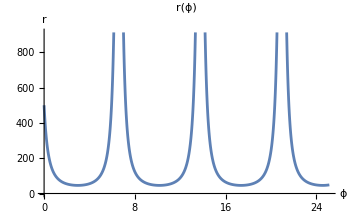

```mathematica
(* Cambio de variable de los coeficientes métricos *)

tablaAdeU=Table[{1/r,AderExt},{r,rtot,20000,1}];
AdeUExt=Interpolation[tablaAdeU][U];

tablaBdeU=Table[{1/r,BderExt},{r,rtot,20000,1}];
BdeUExt=Interpolation[tablaBdeU][U];

tablaAprimedeU=Table[{1/r,AprimederExt},{r,rtot,20000,1}];
AprimedeUExt=Interpolation[tablaAprimedeU][U];

tablaBprimedeU=Table[{1/r,BprimederExt},{r,rtot,20000,1}];
BprimedeUExt=Interpolation[tablaBprimedeU][U];

(*Inversa del radio inicial*)
RadioInicialOrbita=5*10^2;

Uinit=1/RadioInicialOrbita;

(*Seleccionar materia o luz*)
ϵ=1; (*Null->0,Timelike->1*)

If[ϵ==1,
(*Para partículas masivas,energía ligeramente modificada con respecto a la de la órbita circular*)
k= ((1/Uinit)-2*mtot)/Sqrt[(1/Uinit)*((1/Uinit)-3*mtot)];
k=0.999;
(*Para partículas masivas,momento angular de la órbita circular*)
h=(1/Uinit)*Sqrt[(mtot)/((1/Uinit)-3*mtot)];
h=20;
]

If[ϵ==0,
(*Para partículas sin masa*)
k=1;
h=40;
ϕmax=4.15;
]

(*.Cambiar las funciones numéricas de r a ϕ*)
AdeϕExt=AdeUExt/. U->U[ϕ];
BdeϕExt=BdeUExt/. U->U[ϕ];
AprimedeϕExt=AprimedeUExt/. U->U[ϕ];
BprimedeϕExt=BprimedeUExt/. U->U[ϕ];

(*Iniciales*)
AdeϕExtInit=AdeϕExt/. U[ϕ]->Uinit;
BdeϕExtInit=BdeϕExt/. U[ϕ]->Uinit;

(*Definir la ecuación diferencial*)
eq=2*BdeϕExt*U''[ϕ]==-2*U[ϕ]-(k^2/h^2)*(((-1/U[ϕ]^2)*AprimedeϕExt)/AdeϕExt^2)-(((-1/U[ϕ]^2)*BprimedeϕExt)/BdeϕExt)*((1/(AdeϕExt*h^2))*(k^2-AdeϕExt*ϵ^2)-U[ϕ]^2);

If[ϵ==0,initgeod={U[0]==Uinit,U'[0]==Sqrt[Abs[((k^2-AdeϕExtInit*ϵ^2)/(AdeϕExtInit*BdeϕExtInit*h^2))-(U[0]^2/BdeϕExtInit)]],WhenEvent[U[ϕ]<=1/(RadioInicialOrbita+1),{ϕmax=ϕ,Umax=U[ϕ],"StopIntegration",Print["Rayo doblado"]}],WhenEvent[U[ϕ]>=1/rtot,{ϕmax=ϕ,Umax=U[ϕ],"StopIntegration",Print["Colisión"]}]};
(*Resolver numéricamente la ecuación*)
solGeodU=NDSolve[{eq,initgeod},U[ϕ],{ϕ,0,8 Pi},WorkingPrecision->20,MaxSteps->2000000];
]

If[ϵ==1,
ϕmax=30.0*Pi;
initgeod={U[0]==Uinit,U'[0]==Sqrt[Abs[((k^2-AdeϕExtInit*ϵ^2)/(AdeϕExtInit*BdeϕExtInit*h^2))-(U[0]^2/BdeϕExtInit)]],WhenEvent[U[ϕ]>=1/rtot,{ϕmax=ϕ,Umax=U[ϕ],"StopIntegration",Print["Colisión"]}]};
(*Resolver numéricamente la ecuación*)
solGeodU=NDSolve[{eq,initgeod},U[ϕ],{ϕ,0,ϕmax},WorkingPrecision->20,MaxSteps->5000000];
]


Udeϕ[ϕ_]:=Evaluate[U[ϕ]/. solGeodU]
rdeϕ[ϕ_]:=1/Udeϕ[ϕ]

(*Graficar la solución*)
If[ϵ==1,Plot[rdeϕ[ϕ],{ϕ,0,8*Pi},PlotLabel->"r(ϕ)",AxesLabel->{"ϕ","r"}]]

If[ϵ==0,Plot[rdeϕ[ϕ],{ϕ,0,ϕmax},PlotLabel->"r(ϕ)",AxesLabel->{"ϕ","r"}]]

Beep[]
```

## Representación de las órbitas y cálculo de la precesión/deflexión

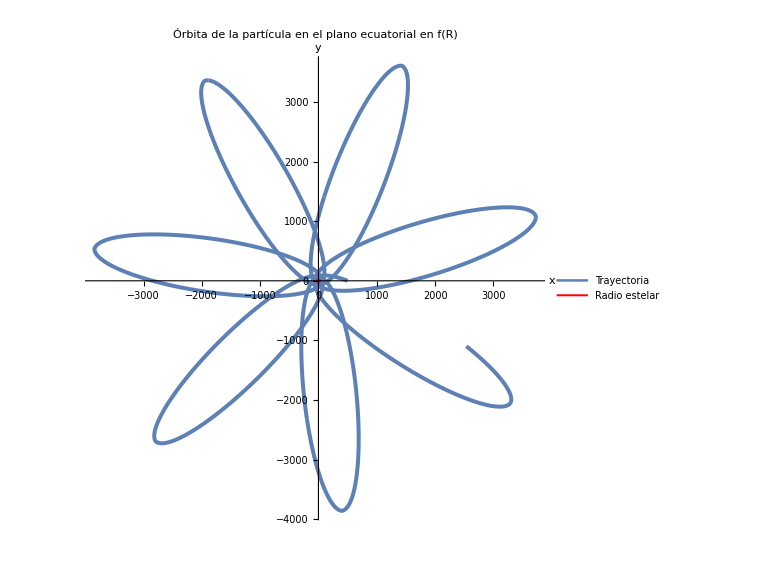

La precesión de la órbita es de 0.906892 radianes, o 51.9611.ba

NDSolve::precw: The precision of the differential equation ({<<1117658336 bytes>>}) is less than WorkingPrecision (20.).

La precesión temporal del perihelio es de 56.538235 grados por segundo

```mathematica
x[ϕ_]:=Cos[ϕ]*rdeϕ[ϕ]
y[ϕ_]:=Sin[ϕ]*rdeϕ[ϕ] 

rtotX=Cos[η]*rtot;
rtotY=Sin[η]*rtot;

trayectoria=ParametricPlot[{x[ϕ][[1]],y[ϕ][[1]]},{ϕ,0,0.529ϕmax},PlotRange->All,PlotStyle->{Thickness[0.005]},ImageSize->Large,AspectRatio->Automatic,AxesLabel->{"x","y"},PlotLegends->{"Trayectoria"},PlotLabel->"Órbita de la partícula en el plano ecuatorial en f(R)",PlotPoints->100000,MaxRecursion->14];

(*
   Lo de la órbita circular
 k=((1/Uinit)-2*mtot)/Sqrt[(1/Uinit)*((1/Uinit)-3*mtot)]
h=(1/Uinit)*Sqrt[(mtot)/((1/Uinit)-3*mtot)]
*)


rtotplot=ParametricPlot[{rtotX,rtotY},{η,0,2*Pi},PlotStyle->{Red,Thickness[0.004]},PlotLegends->{"Radio estelar"}];

Show[trayectoria,rtotplot,AxesOrigin->{0,0}]


(*Calcular la precesión de la órbita*)
If[ϵ==1,
orbita=Table[{ϕ,rdeϕ[ϕ][[1]]},{ϕ,0,ϕmax,ϕmax/100000}];
apocentros=Most[Rest[FindPeaks[orbita[[All,2]]]]];
angulos=orbita[[All,1]][[apocentros[[All,1]]]];
precesiones=Differences[angulos];
precesionPromedio=Mean[precesiones];
precesionModulo=Min[2 Pi-Mod[precesionPromedio,2 Pi],Mod[precesionPromedio,2 Pi]];
Print["La precesión de la órbita es de ",NumberForm[precesionModulo,{Infinity,6}]," radianes, o ", precesionModulo*180/Pi, ".ba"];

soltiempo=NDSolve[{t'[ϕ]==(k/h)*rdeϕ[ϕ][[1]]^2,t[0]==0},t[ϕ],{ϕ,0,ϕmax},WorkingPrecision->20,MaxSteps->2000000];tdeϕ=soltiempo[[1]][[1]]/. Rule->(#2&);
tiempos=tdeϕ[[0]]/@angulos;
periodos=Differences[tiempos];
periodoPromedio=Mean[periodos];
precesionTemporal=(precesionModulo*180/Pi)/(periodoPromedio*3.336*10^-6);
Print["La precesión temporal del perihelio es de ",NumberForm[precesionTemporal,{Infinity,6}], " grados por segundo"];
]

(*Calcular la deflexión de la luz*)
If[ϵ==0,
(*Calcula las derivadas*)
dxdϕ[ϕ_]=D[x[ϕ],ϕ];
dydϕ[ϕ_]=D[y[ϕ],ϕ];
vInicio={dxdϕ[0][[1]],dydϕ[0][[1]]};
vFin={dxdϕ[ϕmax][[1]],dydϕ[ϕmax][[1]]};


(*Calcula el ángulo entre los vectores tangentes*)
productoEscalar=vInicio.vFin;
normaInicio=Norm[vInicio];
normaFin=Norm[vFin];
deflexion=ArcCos[productoEscalar/(normaInicio*normaFin)];
If[ϕmax>2 Pi,deflexion=2 Pi-deflexion];

binfty=Norm[Cross[Append[vInicio,0],{RadioInicialOrbita,0,0}]]/normaInicio;
btan=FindMinValue[{rdeϕ[ϕ][[1]],0<=ϕ<=ϕmax},ϕ];
Print["El parámetro de impacto asintótico es b_infty = ",NumberForm[binfty,{Infinity,6}],"km"];
Print["El parámetro de impacto tangencial es b_tan = ",NumberForm[btan,{Infinity,6}],"km"];
Print["La deflexión de la luz es de ",NumberForm[deflexion,{Infinity,6}]," radianes, o ",NumberForm[deflexion*180/Pi,{Infinity,6}],".ba."];
]
```

## Extracción del valor de h para el caso de luz rasante

```mathematica
ModuloRasante[h_]:=Module[{eq,initgeod,solGeodU,Utan,Udeϕ,rdeϕ,colision,return},
colision=True;
(*Definir la ecuación diferencial*)eq=2*BdeϕExt*U''[ϕ]==-2*U[ϕ]-(k^2/h^2)*(((-1/U[ϕ]^2)*AprimedeϕExt)/AdeϕExt^2)-(((-1/U[ϕ]^2)*BprimedeϕExt)/BdeϕExt)*((1/(AdeϕExt*h^2))*(k^2-AdeϕExt*ϵ^2)-U[ϕ]^2);

initgeod={U[0]==Uinit,U'[0]==Sqrt[Abs[((k^2-AdeϕExtInit*ϵ^2)/(AdeϕExtInit*BdeϕExtInit*h^2))-(U[0]^2/BdeϕExtInit)]],WhenEvent[U[ϕ]<=1/(RadioInicialOrbita+1),{ϕmax=ϕ,Umax=U[ϕ],"StopIntegration",colision=False}],WhenEvent[U[ϕ]>=1/rtot,{ϕmax=ϕ,Umax=U[ϕ],"StopIntegration",colision=True}]};
(*Resolver numéricamente la ecuación*)
solGeodU=NDSolve[{eq,initgeod},U[ϕ],{ϕ,0,8 Pi},WorkingPrecision->20,MaxSteps->1000000];
If[colision,
return=-1,
Utan=FindMaxValue[{solGeodU[[1]][[1]][[2]],0<=ϕ<=ϕmax},ϕ];
return=(1/Utan)-rtot];
return]

(*Método de bisección para el valor inicial de A (Ainit).Se hace uso del módulo anterior,y se busca con una tolerancia ϵ*)
δ=10^-3;
maxIter=30;
iter=0;
inf=rtot;
sup=rtot+10;
While[True,iter=iter+1;
med=(inf+sup)/2;
If[iter>maxIter,Print[Style["AVISO: Alcanzado el número máximo de iteraciones",Red]];Break[]];
If[Abs[ModuloRasante[med]]<δ &&  ModuloRasante[med]>0,Break[],
If[ModuloRasante[med]*ModuloRasante[inf]<0,sup=med,inf=med]
];
];

Print["La luz rasante se da con un valor de h = ",med]
```

NDSolve::precw: The precision of the differential equation ({{2 InterpolatingFunction[{{0.000050001019048792501, <<18>>10}}, <>][U[ϕ]] U''[ϕ] == -2 <<1>> + <<2>>, <<2>>}, <<4>>}) is less than WorkingPrecision (20.).

InterpolatingFunction::dmval: Input value {0.086778826086620605326} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{2 InterpolatingFunction[{{0.000050001019048792501, <<18>>10}}, <>][U[ϕ]] U''[ϕ] == -2 <<1>> + <<2>>, <<2>>}, <<4>>}) is less than WorkingPrecision (20.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

La luz rasante se da con un valor de h = 19.220410030748072655438350492082055

```mathematica
EmitSound[Sound[SoundNote[-60]]]
```

```mathematica
npoints=5000;
Int=Table[{x[ϕ][[1]],y[ϕ][[1]]},{ϕ,0,0.53 ϕmax,(ϕmax-0)/(npoints-1)}];
Export["/Users/neturo/Desktop/orbita_7e-4_0.05.txt",Int,"Table"];
```